```mathematica
(*Programm um die differentielle Zerfallsrate dΓ/ds34, die mit dG_Zc errechnet wurde, zu plotten.*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(*Numerische Werte*)
lam=0.5;lamStep=0.05;eps=0.0005;epsStep=0.0005;mD=1.865;mDs=2.010;mZ=mDs+mD-eps-5epsStep;mPi=0.1396;mJ=3.0969;mGam=0.15;AlpFein=1/137;gJDD=7.44; gDsDPi=17.9;gDDsJPi=gJDD gDsDPi/(2Sqrt[2]);gZc=6.231382;q=Sqrt[4Pi AlpFein];g=Sqrt[6]gDDsJPi/((mZ^2-mJ^2)(1+mJ^2/(2mZ^2)));gZJPi=1;
c=gZJPi q;me=511.0 10^-6;mmu=105.6 10^-3;
numrules={M->mZ,m1->mPi,m2->mJ,m3->mGam,MD->mD,MDs->mDs}
```

{M→3.872,m1→0.1396,m2→3.0969,m3→0.15,MD→1.865,MDs→2.01}

```mathematica
(*Versuche ob aus den Werten dGDs12ds34 die selben Kurven durch Integration mit Mathematica folgen*)
FileEps=500;
FileLam=500;
string0=StringJoin["dGamma_eps",ToString[FileEps],"keV_lam",ToString[FileLam],"MeV.dat"]
plotlabel0=StringJoin["ϵ=",ToString[N[FileEps/1000]]," MeV\nΛ=",ToString[FileLam]," MeV"]
FileEps=5000;
FileLam=500;
string1=StringJoin["dGamma_eps",ToString[FileEps],"keV_lam",ToString[FileLam],"MeV.dat"]
plotlabel1=StringJoin["ϵ=",ToString[N[FileEps/1000]]," MeV\nΛ=",ToString[FileLam]," MeV"]
FileEps=500;
FileLam=800;
string2=StringJoin["dGamma_eps",ToString[FileEps],"keV_lam",ToString[FileLam],"MeV.dat"]
plotlabel2=StringJoin["ϵ=",ToString[N[FileEps/1000]]," MeV\nΛ=",ToString[FileLam]," MeV"]
FileEps=3000;
FileLam=650;
string3=StringJoin["dGamma_eps",ToString[FileEps],"keV_lam",ToString[FileLam],"MeV.dat"]
plotlabel3=StringJoin["ϵ=",ToString[N[FileEps/1000]]," MeV\nΛ=",ToString[FileLam]," MeV"]
FileEps=5000;
FileLam=800;
string4=StringJoin["dGamma_eps",ToString[FileEps],"keV_lam",ToString[FileLam],"MeV.dat"]
plotlabel4=StringJoin["ϵ=",ToString[N[FileEps/1000]]," MeV\nΛ=",ToString[FileLam]," MeV"]
framelabel={"s_31 [GeV^2]","dΓ_3/ds_31 [GeV^-1]"}
```

dGamma_eps500keV_lam500MeV.dat

ϵ=0.5 MeV
Λ=500 MeV

dGamma_eps5000keV_lam500MeV.dat

ϵ=5. MeV
Λ=500 MeV

dGamma_eps500keV_lam800MeV.dat

ϵ=0.5 MeV
Λ=800 MeV

dGamma_eps3000keV_lam650MeV.dat

ϵ=3. MeV
Λ=650 MeV

dGamma_eps5000keV_lam800MeV.dat

ϵ=5. MeV
Λ=800 MeV

{s_31 [GeV^2],dΓ_3/ds_31 [GeV^-1]}

```mathematica
(*Datenwerte Laden, Duplikate aussortieren und fehlerhafte Einträge ignorieren*)
threshold=0;
tG0=DeleteDuplicates[Cases[
Import[ToFileName[NotebookDirectory[],string0],"Table"],{_?NumberQ,_?NumberQ,_?NumberQ,_?(#>threshold&)}]];
tG1=DeleteDuplicates[Cases[
Import[ToFileName[NotebookDirectory[],string1],"Table"],{_?NumberQ,_?NumberQ,_?NumberQ,_?(#>threshold&)}]];
tG2=DeleteDuplicates[Cases[
Import[ToFileName[NotebookDirectory[],string2],"Table"],{_?NumberQ,_?NumberQ,_?NumberQ,_?(#>threshold&)}]];
tG3=DeleteDuplicates[Cases[
Import[ToFileName[NotebookDirectory[],string3],"Table"],{_?NumberQ,_?NumberQ,_?NumberQ,_?(#>threshold&)}]];
tG4=DeleteDuplicates[Cases[
Import[ToFileName[NotebookDirectory[],string4],"Table"],{_?NumberQ,_?NumberQ,_?NumberQ,_?(#>threshold&)}]];
Row[{
ListPointPlot3D[tG0[[All,{1,3,4}]],PlotStyle->Directive[PointSize[Medium],Red]],
ListPointPlot3D[tG1[[All,{1,3,4}]],PlotStyle->Directive[PointSize[Medium],Red]],ListPointPlot3D[tG2[[All,{1,3,4}]],PlotStyle->Directive[PointSize[Medium],Red]],
ListPointPlot3D[tG3[[All,{1,3,4}]],PlotStyle->Directive[PointSize[Medium],Red]],
ListPointPlot3D[tG4[[All,{1,3,4}]],PlotStyle->Directive[PointSize[Medium],Red]],
}]
```

-Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D-

```mathematica
(*Interpolation*)
intG0=Interpolation[tG0[[All,{1,3,4}]],InterpolationOrder->1];
intG1=Interpolation[tG1[[All,{1,3,4}]],InterpolationOrder->1];
intG2=Interpolation[tG2[[All,{1,3,4}]],InterpolationOrder->1];
intG3=Interpolation[tG3[[All,{1,3,4}]],InterpolationOrder->1];
intG4=Interpolation[tG4[[All,{1,3,4}]],InterpolationOrder->1];
```

```mathematica
(*Kaellen Funktion*)
Kaellen[x_,y_,z_]:=x^2+y^2+z^2-2x y-2x z-2y z
```

```mathematica
(*Phasenraumgrenzen*)
s31p=(M-m2)^2//.numrules;
s31m=(m1+m3)^2//.numrules;
s12p[s31_]:=m1^2+m2^2-1/(2 s31)((s31-M^2+m2^2)(s31+m1^2-m3^2)-Kaellen[s31,M^2,m2^2]^(1/2)Kaellen[s31,m1^2,m3^2]^(1/2))//.numrules
s12m[s31_]:=m1^2+m2^2-1/(2 s31)((s31-M^2+m2^2)(s31+m1^2-m3^2)+Kaellen[s31,M^2,m2^2]^(1/2)Kaellen[s31,m1^2,m3^2]^(1/2))//.numrules
```

```mathematica
(*Datenwerte interpolieren*)
intpoints=(s31p-s31m)/500
dGds0[s31_]:=NIntegrate[{intG0[s12,s31]},{s12,Re[s12m[s31]],Re[s12p[s31]]}]
dGds1[s31_]:=NIntegrate[{intG1[s12,s31]},{s12,Re[s12m[s31]],Re[s12p[s31]]}]
dGds2[s31_]:=NIntegrate[{intG2[s12,s31]},{s12,Re[s12m[s31]],Re[s12p[s31]]}]
dGds3[s31_]:=NIntegrate[{intG3[s12,s31]},{s12,Re[s12m[s31]],Re[s12p[s31]]}]
dGds4[s31_]:=NIntegrate[{intG4[s12,s31]},{s12,Re[s12m[s31]],Re[s12p[s31]]}]
tdG0=Table[{s31,dGds0[s31]},{s31,s31m,s31p,intpoints}]//Quiet;
tdG1=Table[{s31,dGds1[s31]},{s31,s31m,s31p,intpoints}]//Quiet;
tdG2=Table[{s31,dGds2[s31]},{s31,s31m,s31p,intpoints}]//Quiet;
tdG3=Table[{s31,dGds3[s31]},{s31,s31m,s31p,intpoints}]//Quiet;
tdG4=Table[{s31,dGds4[s31]},{s31,s31m,s31p,intpoints}]//Quiet;
```

0.00103382

```mathematica
(*Interpolation der Integriereten Datenwerte*)
idG0=Interpolation[Cases[tdG0,{_?NumberQ,{_?(#>0&)}}],InterpolationOrder->1]
idG1=Interpolation[Cases[tdG1,{_?NumberQ,{_?(#>0&)}}],InterpolationOrder->1]
idG2=Interpolation[Cases[tdG2,{_?NumberQ,{_?(#>0&)}}],InterpolationOrder->1]
idG3=Interpolation[Cases[tdG3,{_?NumberQ,{_?(#>0&)}}],InterpolationOrder->1]
idG4=Interpolation[Cases[tdG4,{_?NumberQ,{_?(#>0&)}}],InterpolationOrder->1]
```

InterpolatingFunction[{{0.084902,0.599746}},<>]

InterpolatingFunction[{{0.084902,0.595611}},<>]

InterpolatingFunction[{{0.084902,0.599746}},<>]

InterpolatingFunction[{{0.084902,0.599746}},<>]

InterpolatingFunction[{{0.084902,0.595611}},<>]

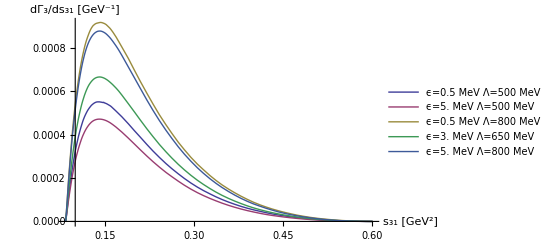

-Graphics-

```mathematica
(*Datenwerte plotten*)
Plot[{idG0[s31],idG1[s31],idG2[s31],idG3[s31],idG4[s31]},{s31,s31m,s31p},AxesLabel->framelabel,PlotLegends->{
Text[Style[plotlabel0,FontSize->13]],
Text[Style[plotlabel1,FontSize->13]],
Text[Style[plotlabel2,FontSize->13]],
Text[Style[plotlabel3,FontSize->13]],
Text[Style[plotlabel4,FontSize->13]]}]//Quiet
output=LogPlot[{idG0[s31],idG1[s31],idG2[s31],idG3[s31],idG4[s31]},{s31,s31m,s31p},
FrameLabel->framelabel,
LabelStyle->{FontSize->18},
PlotRange->{10^-7,2 10^-3},
PlotLegends->Placed[
LineLegend[
{Text[Style[plotlabel0,FontSize->13]],
Text[Style[plotlabel1,FontSize->13]],
Text[Style[plotlabel2,FontSize->13]],
Text[Style[plotlabel3,FontSize->13]],
Text[Style[plotlabel4,FontSize->13]]},
LegendLayout->{"Row",1}],{Above,Top}],
Frame->True,
Filling->{2->{{3},Directive[Opacity[0.2],Purple]}},
ImageSize->500]//Quiet
```

```mathematica
Export["dGammads31.eps",output,ImageResolution->400]
```

dGammads31.eps